#### INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb.

#### Use the Tmat stored in BC_CumulativeBeta.nb

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatBrownNew

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

10-30-2023 22:59

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

### Run Sections 1 and 2 of BC_CumulativeBeta.nb, but with just the OutputFors that you will need.

### Elastic maps, not just at nodes.

```mathematica
SmatOfPt[pt_,Tmat_,dt_,Σn_,pw_]:=(1-TofPt[pt,dt]) SmatOfΣ[Σ1ofPt[pt,dt],Tmat,Σn,pw]+   
                                                                                        TofPt[pt,dt]   SmatOfΣ[Σ2ofPt[pt,dt],Tmat,Σn,pw]     (* Σn plays no role for pw = pw2 or pw = pw4 *)
```

#### Example, assuming you have run the OutputFors for pw2.

Tmat is TmatBrownNew

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

pt = {0.,1.5}  (blue circle)

t = 1.

{Σ1, Σ2} = {TRIV,MONO}

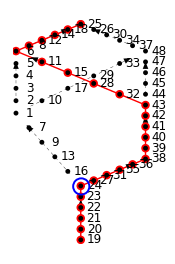

Smat at pt is (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)

```mathematica
Print[MatrixNote[Tmat]];
Print["Path nodes are ",Σn/@domain[Σn]];
Print["dt = ",dt];
Print["pt = ",pt=PointsOnPath[Σn,dt][[6]],"  (blue circle)"];
Print["t = ",TofPt[pt,dt]];
Print["{Σ1, Σ2} = ",{Σ1ofPt[pt,dt],Σ2ofPt[pt,dt]}];
Show[{LatticeWithPts[dt,Σn],Graphics[{Blue,Thickness[.008],Circle[pt,.15]}]},ImageSize->175]
Print["Smat at pt is ",MatrixForm[SmatOfPt[pt,Tmat,dt,dummy,pw2]]];
```

### Beta curves diagram

```mathematica
βT[Tmat_,Σ_]:=999Degree;   (* This should have been entered in FindSymGroupsForPublic *)
βofPathPt[pt_,Tmat_,dt_,Σn_,pw_,Σ_]:=βT[SmatOfPt[pt,Tmat,dt,Σn,pw],Σ];  (* Measures how far the elastic map at pt = (x,y) is from having symmetry Σ *)
Beta8tuple[pt_,Tmat_,dt_,Σn_,pw_]:=βofPathPt[pt,Tmat,dt,Σn,pw,#]&/@ListSigmaAll;
```

#### As functions of integer j. The integer j will give the point (j, 0) on the horizontal axis in the Beta curve diagrams. It runs over 1, 2, 3, ..., Length[path].

```mathematica
βofJ[j_,Σn_,Tmat_,dt_,pw_,Σ_]:=βofPathPt[PathPtOfJ[j,Σn,dt],Tmat,dt,Σn,pw,Σ];  (* Measures how far the elastic map at j is from having symmetry Σ *)
BetaPoints[Σn_,Tmat_,dt_,pw_,Σ_]:=Table[{j,βofJ[j,Σn,Tmat,dt,pw,Σ]/Degree},{j,1,Length[PointsOnPath[Σn,dt]]}](* vertical coordinate is in degrees *);
```

```mathematica
VerticalLineAtJ[j_,Σn_,Tmat_,dt_,pw_,Σ_]:=Line[{{j,0},{j,βofJ[j,Σn,Tmat,dt,pw,Σ]/Degree}}];   (* vertical coordinate is in degrees *)VerticalLinesForΣ[Σn_,Tmat_,dt_,pw_,Σ_]:=VerticalLineAtJ[#,Σn,Tmat,dt,pw,Σ]&/@Select[Range[Length[PointsOnPath[Σn,dt]]],jIsNode[#,Σn,dt]&];
```

#### Optional: Determine the scale for the y-value of the custom tick labels on the x-axis

```mathematica
ΣLast=ListΣ[[Length[ListΣ]]]
βofJ[1,Σn,Tmat,dt,pw,ISO]/Degree
```

ISO

26.0366

```mathematica
yText[Tmat_,dt_,Σn_,pw_,ListΣ_]:=Max[βofJ[1,Σn,Tmat,dt,pw,#]&/@ListΣ]/Degree;
yran=yText[Tmat,dt,Σn,pw,ListΣ]
```

26.0366

#### MAIN BETA CURVE DIAGRAM The last text command places a label like β_XISO^ (15.98) at the far left of the plot

```mathematica
Clear[BetaCurvesDiagram]
```

```mathematica
ptsz=0.013;
yticks = Automatic; (* yticks =Range[0,50,5]; *)
BetaCurvesDiagram[Σn_,Tmat_,dt_,pw_,ListΣ_]:=Graphics[{PointSize[ptsz],
{hue[#],
Point/@BetaPoints[Σn,Tmat,dt,pw,#],
Line[BetaPoints[Σn,Tmat,dt,pw,#]]}&/@ListΣ, (* colored segmented beta curves *)
{Dashing[{.01,.02}],VerticalLinesForΣ[Σn,Tmat,dt,pw,#]&/@ListΣ}, (* vertical lines *)
Text[Style[position[PointsOnPath[Σn,dt][[#]],dt],12],{#,-0.04 yText[Tmat,dt,Σn,pw,ListΣ]}]&/@Range[Length[PointsOnPath[Σn,dt]]], (* integer tick label (e.g., 8) *) 
Text[Style[ΣofJ[#,Σn,dt],11],{#,-0.08 yText[Tmat,dt,Σn,pw,ListΣ]}]&/@JlistForNodes[Σn,dt], (* tick label as path entry (e.g., TET) *)
Text[Style[SequenceForm[BetaText[#]," (",Round[βofJ[1,Σn,Tmat,dt,pw,#]/Degree,0.01],")"],{hue[#],13}], (* the text *)
                                                           {-0.05 Length[PointsOnPath[Σn,dt]],βofJ[1,Σn,Tmat,dt,pw,#]/Degree},{1,0}]&/@ListΣ, (* the location of the text *)
Text[Style[SequenceForm["β_Σ, degrees"," [",pw,"]"],18],{1-0.35Length[PointsOnPath[Σn,dt]],.5yText[Tmat,dt,Σn,pw,ListΣ]},{0,0},{0,1}]  (* y-axis label *)
},  
Axes->True,Ticks->{None,yticks},AxesOrigin->{0,0},TicksStyle->12,AspectRatio->0.8,ImageSize->600]
```

```mathematica
BetaPointsDiff[Σn_,Tmat_,dt_,pwA_,pwB_,Σ_]:=Table[{j,βofJ[j,Σn,Tmat,dt,pwA,Σ]/Degree-βofJ[j,Σn,Tmat,dt,pwB,Σ]/Degree},{j,1,Length[PointsOnPath[Σn,dt]]}];
```

```mathematica
BetaCurvesDiffDiagram[Σn_,Tmat_,dt_,pwA_,pwB_,ListΣ_]:=Graphics[{PointSize[ptsz],
{hue[#],
Point/@BetaPointsDiff[Σn,Tmat,dt,pwA,pwB,#],
Line[BetaPointsDiff[Σn,Tmat,dt,pwA,pwB,#]]}&/@ListΣ}, (* colored segmented beta curves *)
Axes->True,Ticks->{None,Automatic},AxesOrigin->{0,0},TicksStyle->12,AspectRatio->1,ImageSize->500]
```

#### KEY COMMAND: Specify the beta curves to be plotted.

```mathematica
ListΣ={ORTH,ISO};
```

```mathematica
ListΣ={XISO};
```

```mathematica
ListΣ={TET};
```

```mathematica
ListΣ={MONO,ORTH,TET,TRIG,XISO,CUBE,ISO};
```

#### KEY COMMAND: choose pw2 or pw3

```mathematica
pw=pw3;
```

```mathematica
pw=pw4;
```

```mathematica
pw=pw2;
```

```mathematica
RunPts[pw_]:=If[pw===pw2,AllPoints[dt],PointsOnPath[Σn,dt]]
(* If[pw===pw2,RunPts=AllPoints[dt],RunPts=PointsOnPath[Σn,dt]]; *)
```

```mathematica
RunPts[pw2]
RunPts[pw3]
RunPts[pw4]
```

{{-1.2,2.85},{-1.2,3.08},{-1.2,3.31},{-1.2,3.54},{-1.2,3.77},{-1.2,4.},{-0.96,2.58},{-0.96,4.1},{-0.72,2.31},{-0.72,3.08},{-0.72,3.8},{-0.72,4.2},{-0.48,2.04},{-0.48,4.3},{-0.24,3.6},{-0.24,1.77},{-0.24,3.31},{-0.24,4.4},{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.,4.5},{0.24,4.4},{0.24,1.6},{0.24,3.4},{0.24,3.54},{0.48,4.3},{0.48,1.7},{0.72,3.2},{0.72,3.77},{0.72,4.2},{0.72,1.8},{0.96,1.9},{0.96,4.1},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{1.2,3.2},{1.2,3.4},{1.2,3.6},{1.2,3.8},{1.2,4.}}

{{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.24,1.6},{0.48,1.7},{0.72,1.8},{0.96,1.9},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{0.72,3.2},{0.24,3.4},{-0.24,3.6},{-0.72,3.8},{-1.2,4.},{-0.96,4.1},{-0.72,4.2},{-0.48,4.3},{-0.24,4.4},{0.,4.5}}

{{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.24,1.6},{0.48,1.7},{0.72,1.8},{0.96,1.9},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{0.72,3.2},{0.24,3.4},{-0.24,3.6},{-0.72,3.8},{-1.2,4.},{-0.96,4.1},{-0.72,4.2},{-0.48,4.3},{-0.24,4.4},{0.,4.5}}

#### OutputAllPts[Sigma] will give the beta values for the specified Sigma and for all the points.

```mathematica
OutputAllPts[Σ_,pw_]:=OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],Σ]&/@RunPts[pw] ;
(* Σn plays no role for pw = pw2 or pw = pw4 *)
```

#### KEY COMPUTATION: Run OutputFor for whatever pw you want and whatever Sigmas you want for beta curves. By default, this will run all three pw and the full set of Sigmas.

```mathematica
WantDetails="noWantDetails"
```

noWantDetails

```mathematica
ListΣ
```

{MONO,ORTH,TET,TRIG,XISO,CUBE,ISO}

```mathematica
OutputAllPts[#,pw2]&/@ListΣ
```

```mathematica
OutputAllPts[#,pw3]&/@ListΣ
```

```mathematica
OutputAllPts[#,pw4]&/@ListΣ
```

```mathematica
(* OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],MONO]&/@RunPts
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],ORTH]&/@RunPts   
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],TET]&/@RunPts  
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],XISO]&/@RunPts  
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],ISO]&/@RunPts
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],TRIG]&/@RunPts
OutputFor[SmatOfPt[#,Tmat,dt,Σn,pw],CUBE]&/@RunPts *)
```

## Beta curves plotting

#### One beta curve

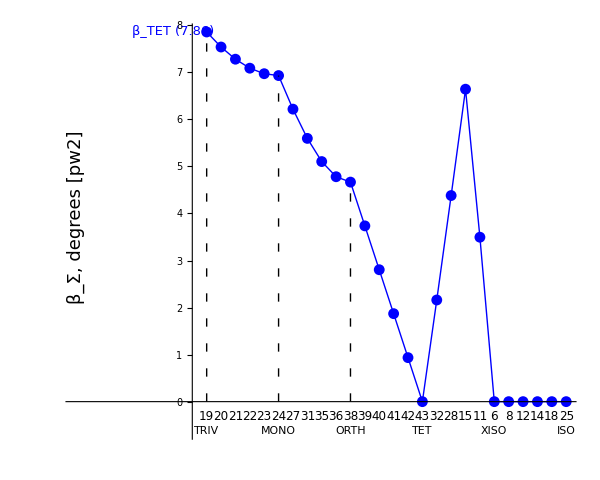

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,pw,{TET}]
```

#### Main plot

Tmat is TmatBrownNew

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

pw = pw2

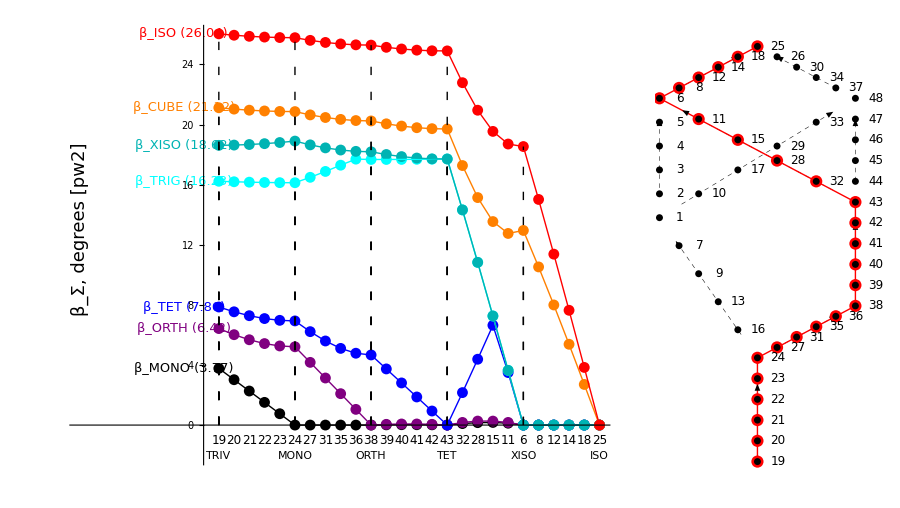

```mathematica
Print[MatrixNote[Tmat]];
Print["Path nodes are ",Σn/@domain[Σn]];
Print["dt = ",dt];
Print["pw = ",pw];
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,pw,ListΣ],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Three node sequences for pw2 (based on AllPoints)

-Graphics-

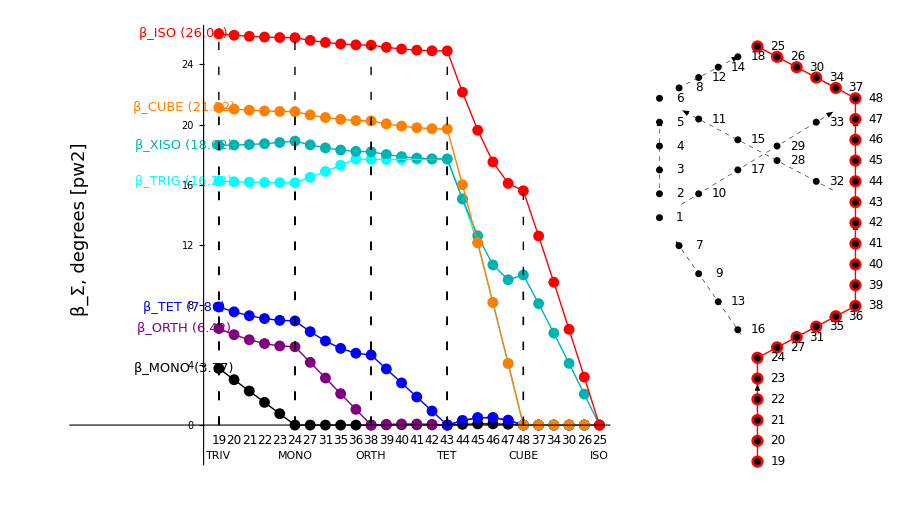

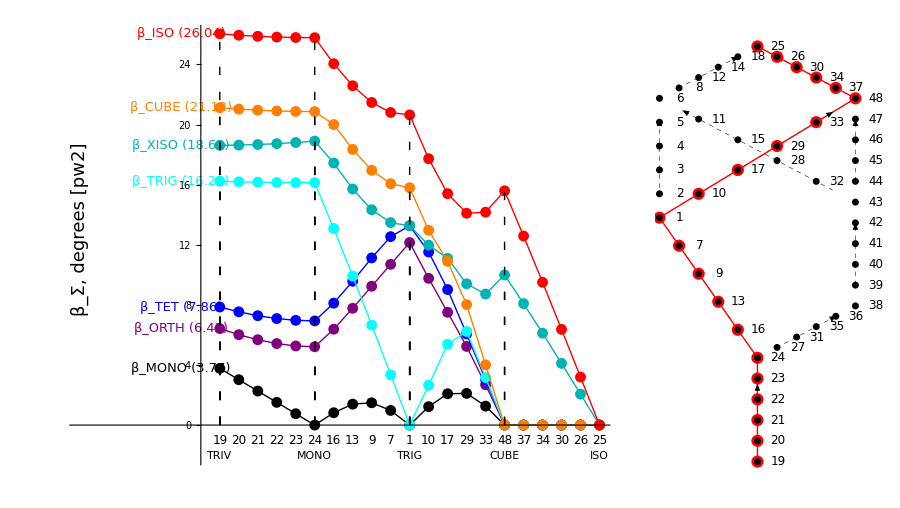

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnBC,Tmat,dt,pw2,ListΣ],
LatticeWithPts[dt,ΣnBC]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnCUBE,Tmat,dt,pw2,ListΣ],
LatticeWithPts[dt,ΣnCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIG,Tmat,dt,pw2,ListΣ],
LatticeWithPts[dt,ΣnTRIG]},ImageSize->900,Spacings->0]
```

#### pw2, pw3, pw4

-Graphics-

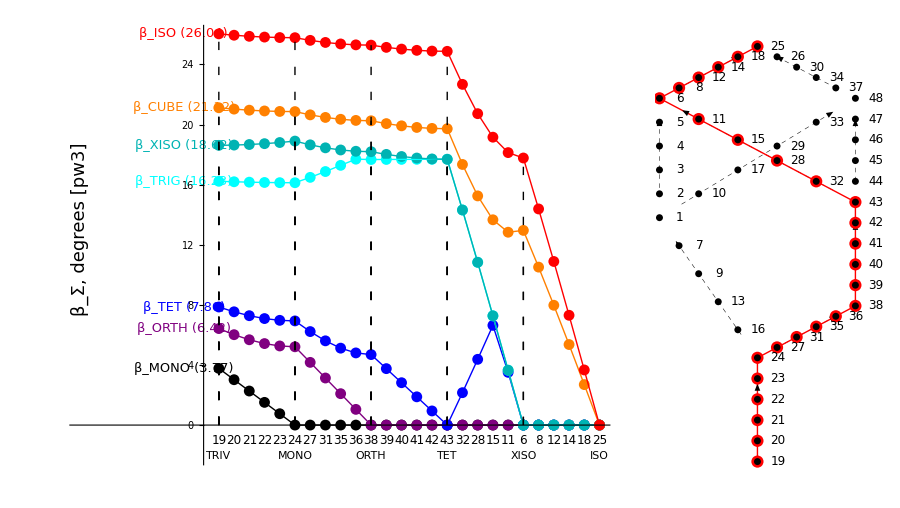

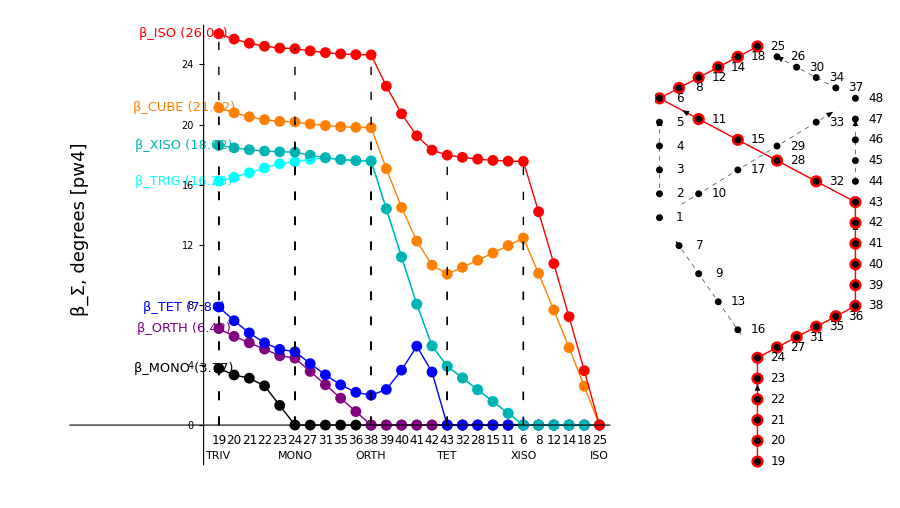

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,pw2,ListΣ],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,pw3,ListΣ],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,pw4,ListΣ],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Examples

```mathematica
BetaPoints[Σn,Tmat,dt,pw2,MONO]
```

{{1,3.77222},{2,3.01934},{3,2.26542},{4,1.51072},{5,0.755492},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0.0157242},{13,0.0237448},{14,0.0238425},{15,0.0159182},{16,0},{17,0.099143},{18,0.161491},{19,0.17443},{20,0.124143},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0}}

#### Compare beta curves for pw2 and pw3

{{1,3.77222},{2,3.01934},{3,2.26542},{4,1.51072},{5,0.755492},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0.0157242},{13,0.0237448},{14,0.0238425},{15,0.0159182},{16,0},{17,0.099143},{18,0.161491},{19,0.17443},{20,0.124143},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0}}

{{1,3.77222},{2,3.01934},{3,2.26542},{4,1.51072},{5,0.755492},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0}}

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0.0157242},{13,0.0237448},{14,0.0238425},{15,0.0159182},{16,0},{17,0.099143},{18,0.161491},{19,0.17443},{20,0.124143},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0}}

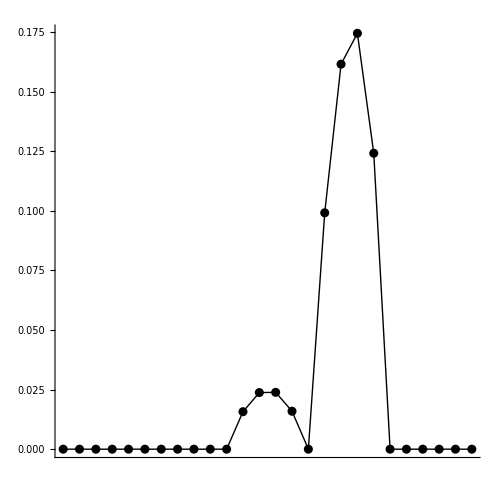

```mathematica
Σ = MONO;pwA=pw2;pwB=pw3;
BetaPoints[Σn,Tmat,dt,pwA,Σ]
BetaPoints[Σn,Tmat,dt,pwB,Σ]
BetaPointsDiff[Σn,Tmat,dt,pwA,pwB,Σ]
BetaCurvesDiffDiagram[Σn,Tmat,dt,pwA,pwB,{Σ}]
```

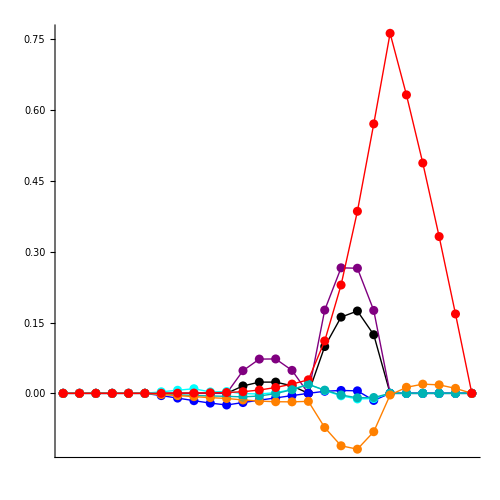

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,pw2,pw3,ListΣ]
```

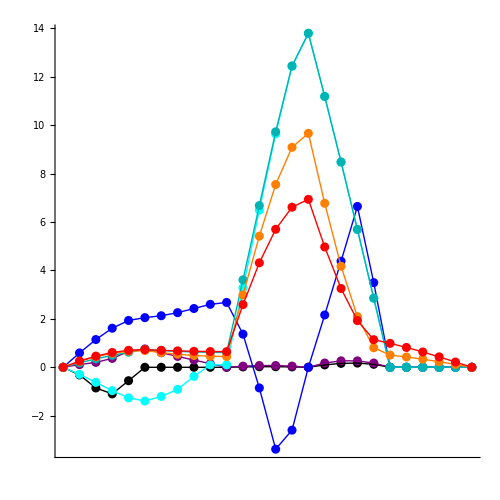

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,pw2,pw4,ListΣ]
```

#### Any 999s in the 8-tuples/Degree mean you have not run all OutputFor (or that we still have a bug). When you run the lattice for the first time you will see lots of 999s.

0.2

Tmat is TmatBrownNew

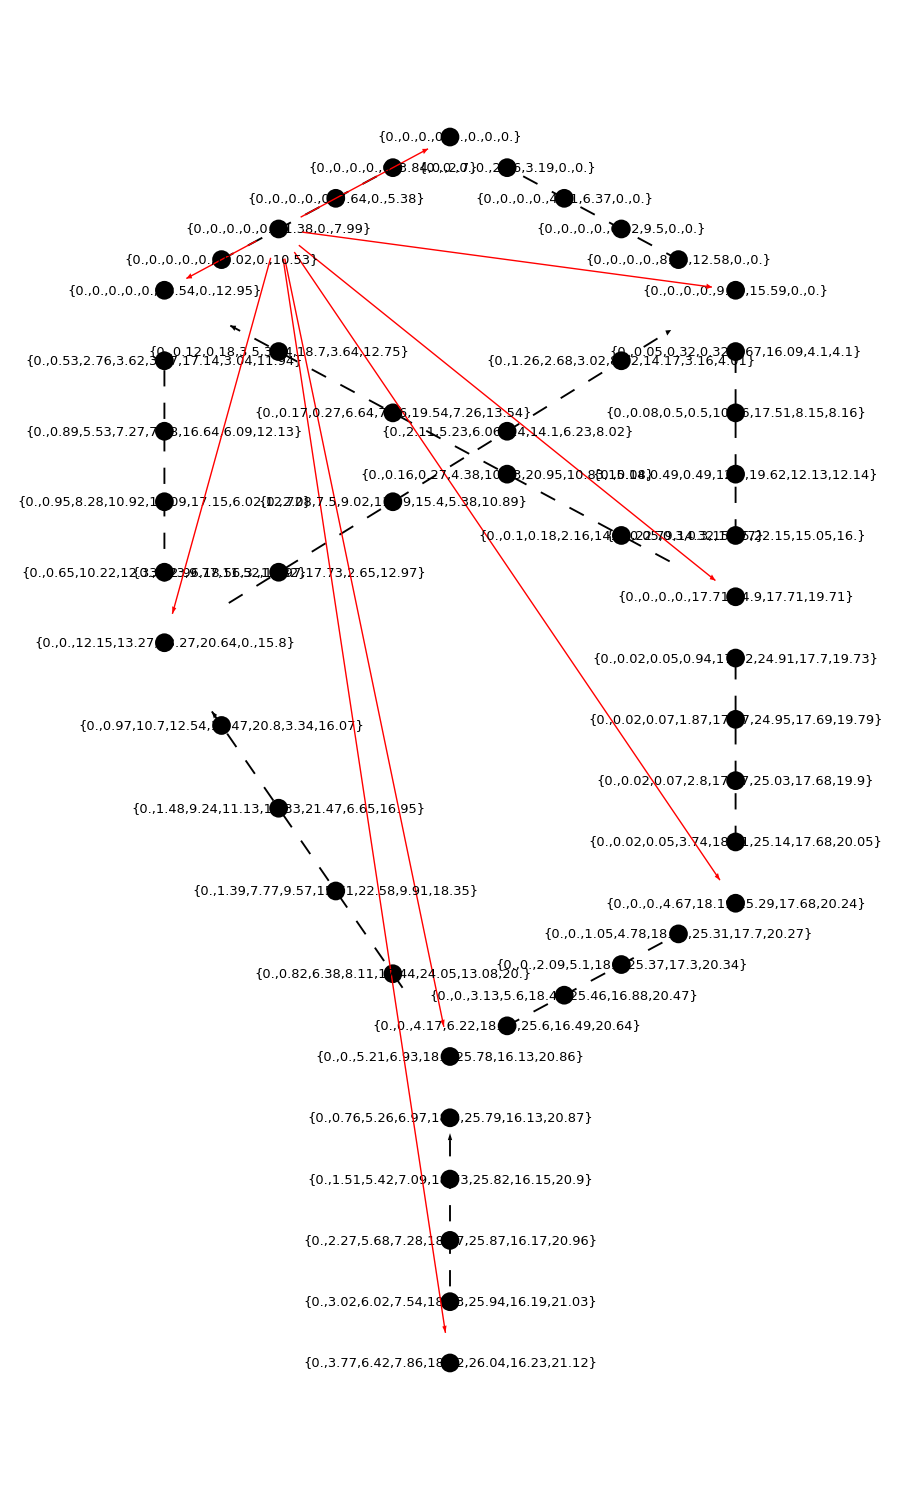

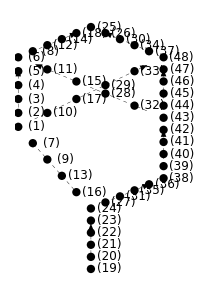

```mathematica
dt
pickpoint=12;
MatrixNote[Tmat]
Graphics[{LatticeBlank,PointSize[.015],
Point/@AllPoints[dt],
{Red,
Arrow[{AllPoints[dt][[pickpoint]],NodePt[#]},.1]&/@ListSigmaAll},
If[True,Text[Style[Round[Beta8tuple[#,Tmat,dt,Σn,pw2]/Degree,.01],13],#,{-1.15,0}]&/@AllPoints[dt]]},ImageSize->900]
Graphics[{LatticeBlank,PointSize[.03],
Point/@AllPoints[dt],
Text[Style[Position[AllPoints[dt],#],12],#+{.3,0}]&/@AllPoints[dt]},ImageSize->200]
```

## For Reference: BrownNew

#### Three node sequences for pw2 (based on AllPoints): BC, CUBE, TRIG

-Graphics-

-Graphics-

-Graphics-

#### pw2, pw3, pw4

-Graphics-

-Graphics-

-Graphics-

#### Compare beta curves for pw2 and pw3

-Graphics-

-Graphics-

-Graphics-